# 双曲线

sec(t)=1/(cos(t))

```mathematica
Manipulate[ParametricPlot[{a Sec[t],b Tan[t]},{t,0,θ},Exclusions->{π/2,(3π)/2},PlotRange->({-1,1}#&)/@{2π,2π}],{a,1,2},{b,1,2},{{θ,2π},0.01,2π}]
```

### 什么是双曲正弦sinh，双曲余弦cosh

```mathematica
Manipulate[Show[(*双曲线*)ParametricPlot[{Sec[t],Tan[t]},{t,0,2π},Exclusions->{π/2,(3π)/2},PlotRange->({-1,1}#&)/@{2π,2π}],
(*参考点线*)Graphics[p={Sec[t1],Tan[t1]};px=ReplacePart[p,2->0];py=ReplacePart[p,1->0];{Circle[],HalfLine[{0,0},p],Magenta,PointSize[Medium],Point[{px,py,p}],Annotation[Line[{px,p,py}],"Sinh"]}]],{{t1,π/3},0,2π}]
```

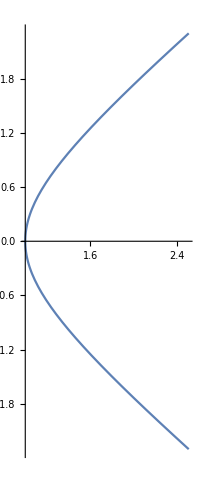

```mathematica
Manipulate[ParametricPlot[{Cosh[t],Sinh[t]},{t,-π/2,π/2}],{θ,0.01,π/2}]
```

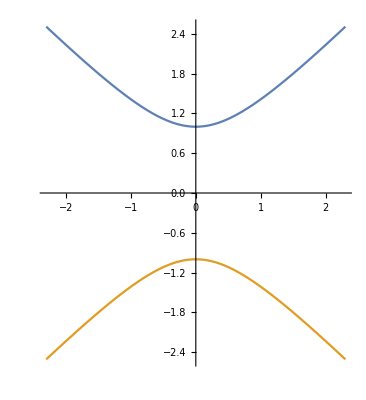

```mathematica
ParametricPlot[{{Sinh[t],Cosh[t]},{Sinh[t],-Cosh[t]}},{t,-π/2,π/2}]
```

```mathematica
Manipulate[Plot[Sinh[t],{t,-k π,k π},ImageSize->Medium],{{k,1},0,5}]
```

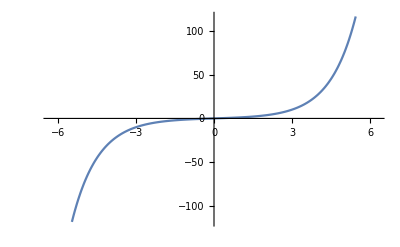

```mathematica
Plot[Sinh[t],{t,-2π,2π}]
```

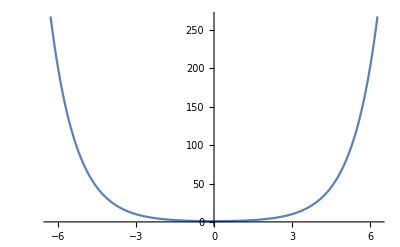

```mathematica
Plot[Cosh[t],{t,-2π,2π}]
```

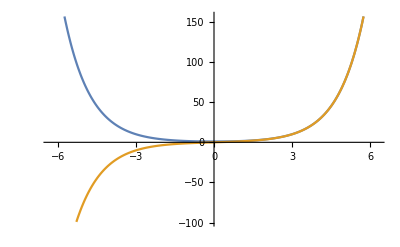

```mathematica
Plot[{Cosh[t],Sinh[t]},{t,-2π,2π}]
```

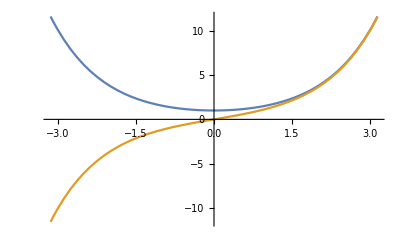

```mathematica
Plot[{Cosh[t],Sinh[t]},{t,-π,π}]
```